```mathematica
SetDirectory[NotebookDirectory[]];
options3={Frame->{True,True,False,False},FrameStyle->Black,BaseStyle->{FontSize->30},LabelStyle->Black};
```

```mathematica
fNumericMean[aX_,α_,β_,y0_]:=Module[{y,x,f=NDSolveValue[{y'[x]==α y[x](1-β y[x]),y[0]==y0},y,{x,0,100}]},f[aX]]
fMean[x_,α_,β_,y0_]:=(ⅇ^(x α) y0)/(1-y0 β+ⅇ^(x α) y0 β)
fYGenerate[x_,α_,β_,y0_,σ_]:=RandomVariate[NormalDistribution[fMean[x,α,β,y0],σ],{1}][[1]]
```

```mathematica
lX =Table[x,{x,0,10,0.5}];
lY=fYGenerate[#,0.5,0.001,5,2]&/@lX;
```

## Get fake data

```mathematica
Needs["PolygonPlotMarkers`"]

allShapes=PolygonMarker[All]
Tooltip[Graphics[{FaceForm[Hue@Random[]],EdgeForm[{Black,Thickness[0.003],JoinForm["Miter"]}],PolygonMarker[#,1]},ImageSize->30,PlotRange->1.5,PlotRangePadding->0,ImagePadding->0],#]&/@allShapes
```

{TripleCross,UpTriangle,UpTriangleTruncated,DownTriangle,DownTriangleTruncated,LeftTriangle,LeftTriangleTruncated,RightTriangle,RightTriangleTruncated,ThreePointedStar,Cross,DiagonalCross,Diamond,Square,FourPointedStar,DiagonalFourPointedStar,FivefoldCross,Pentagon,FivePointedStar,FivePointedStarThick,SixfoldCross,Hexagon,SixPointedStar,SixPointedStarSlim,SevenfoldCross,SevenPointedStar,SevenPointedStarNeat,SevenPointedStarSlim,EightfoldCross,Circle}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
lX =Table[x,{x,0,10,0.5}];
lY=fYGenerate[#,0.5,0.05,5,2]&/@lX;
lY1=fYGenerate[#,0.5,0.05,5,2]&/@lX;
lY2=fYGenerate[#,0.5,0.05,5,2]&/@lX;
```

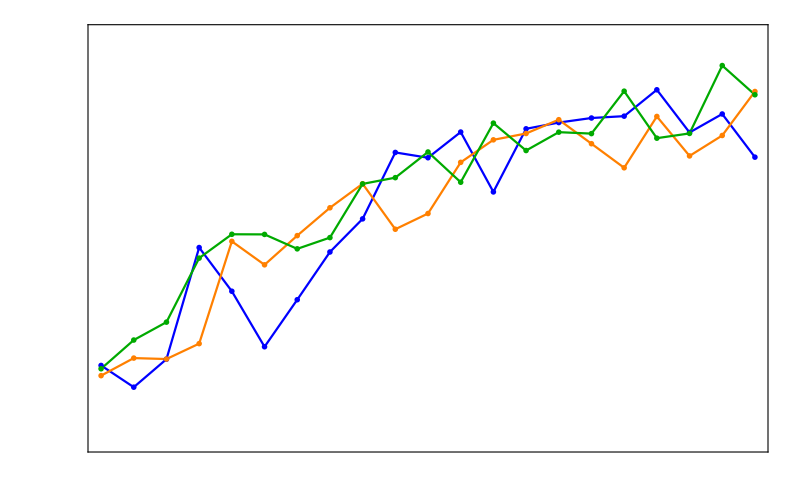

```mathematica
g1=ListLinePlot[{Thread[{lX,lY}],Thread[{lX,lY1}],Thread[{lX,lY2}]},PlotStyle->{Blue,Orange,Darker@Green},FrameStyle->Directive[Black,16,Thick],PlotRange->{Automatic,{0,25}},Evaluate@options3,PlotMarkers ->{Graphics[{FaceForm[Blue],Disk[{0,0},Scaled[0.05/Sqrt[π]]]},AlignmentPoint->{0,0}],Graphics[{FaceForm[Orange],Disk[{0,0},Scaled[0.05/Sqrt[π]]]},AlignmentPoint->{0,0}],
Graphics[{FaceForm[Darker@Green],Disk[{0,0},Scaled[0.05/Sqrt[π]]]},AlignmentPoint->{0,0}]},FrameLabel->None,ImageSize->800,FrameTicks->None]
```

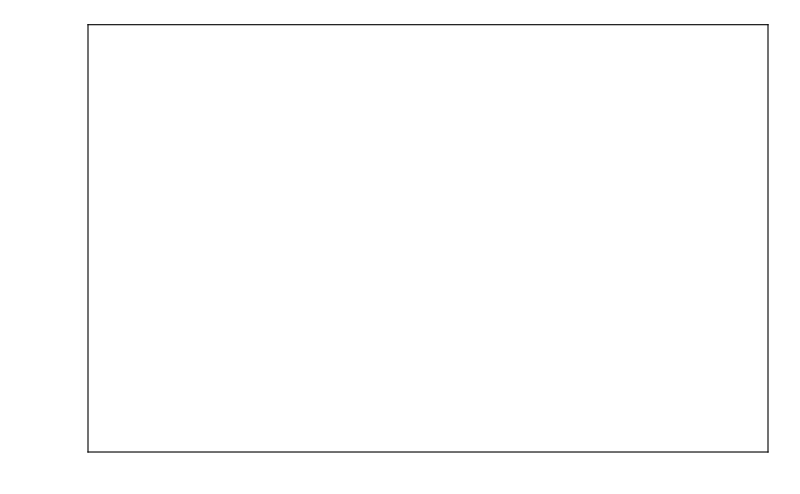

```mathematica
g1a=ListPlot[Thread[{lX,lY}],PlotStyle->{{Thickness[0.01],White},{Thickness[0.01],Orange},{Thickness[0.01],Magenta}},PlotRange->{Automatic,{0,25}},Evaluate@options3,PlotMarkers ->{Automatic,15},FrameLabel->None,ImageSize->800,FrameTicks->None]
```

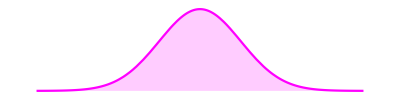

```mathematica
aPlot=Plot[PDF[NormalDistribution[0,1],x],{x,-4,4},Axes->None,PlotStyle->Magenta,Filling->Bottom,AspectRatio->1/4]
```

```mathematica
aPlot1=Plot[PDF[NormalDistribution[0,2],x],{x,-6,6},Axes->None,PlotStyle->Magenta,Filling->Bottom,AspectRatio->1/4];
aPlot2=Plot[PDF[NormalDistribution[0,0.5],x],{x,-4,4},Axes->None,PlotStyle->Magenta,Filling->Bottom,AspectRatio->1/4];
```

```mathematica
g2=Show[g1a,Graphics[Inset[Rotate[aPlot1,3Pi /2],{1,fMean[1,0.5,0.05,5]}]],
Graphics[Inset[Rotate[aPlot,3 Pi/2],{1+2.67,fMean[1+2.7,0.5,0.05,5]}]],Graphics[Inset[Rotate[aPlot,3 Pi/2],{1+2.7 2,fMean[7,0.5,0.05,5]}]],Graphics[Inset[Rotate[aPlot2,3 Pi/2],{9.5,19.4}]],FrameStyle->Directive[Black,16,Thick]]
```

-Graphics-

```mathematica
Export["../figures/logistic_full.pdf",g1]
Export["../figures/logistic_summary.pdf",g2]
```

../figures/logistic_full.pdf

../figures/logistic_summary.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["../figures/logistic_summary.pdf"]]]
```

## Plot deterministic solution

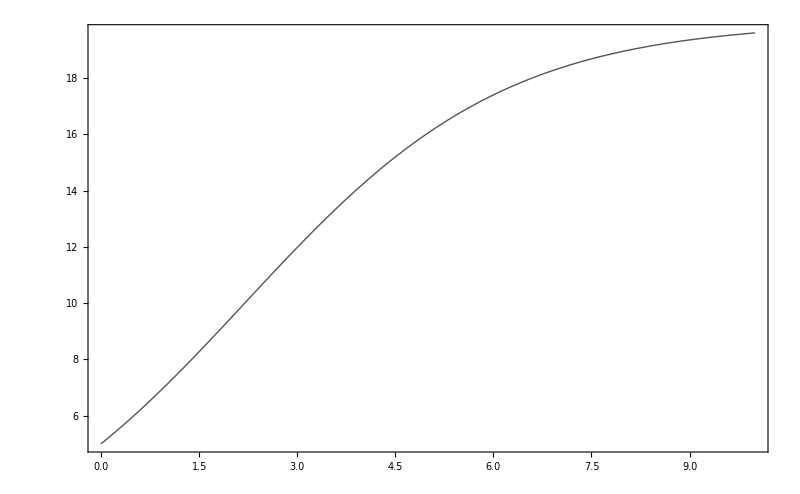

```mathematica
g1=Plot[fMean[x,0.5,0.05,5],{x,0,10},FrameLabel->None,ImageSize->800,FrameTicks->None,FrameStyle->Directive[Black,16,Thick],Frame->{True,True,False,False},PlotStyle->Directive[Thick,Darker@Gray]]
```

```mathematica
true=Table[fMean[x,0.5,0.05,5],{x,0,10,0.01}];
trueNoise=true+RandomVariate[NormalDistribution[0,1],Length@true];
```

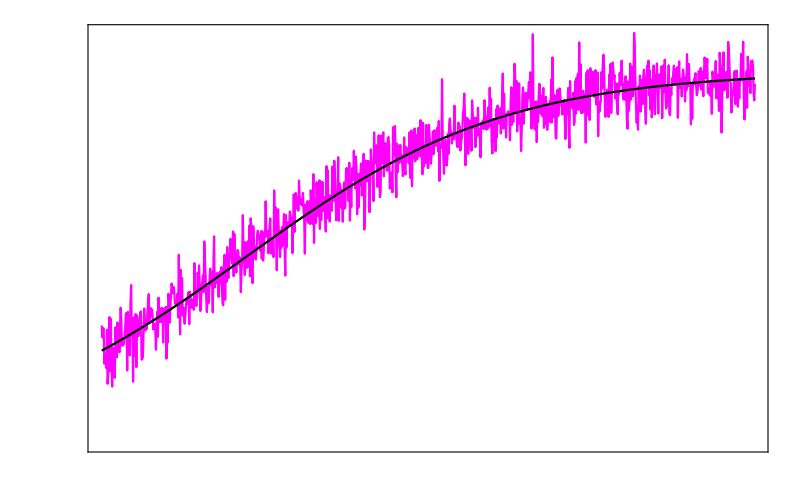

```mathematica
ListLinePlot[{trueNoise,true},Axes->None,PlotStyle->{Magenta,Black},FrameLabel->None,ImageSize->800,FrameTicks->None,FrameStyle->Directive[Black,16,Thick],Frame->{True,True,False,False},PlotStyle->Directive[Thick,Darker@Gray]]
```

```mathematica
Clear[fPDF]
```

```mathematica
fPDF[y_,x_,α_,β_,y0_,fSigma_]:=PDF[NormalDistribution[fMean[x,α,β,y0],fSigma[x]],y]
```

```mathematica
fSigma[x_]:=1
```

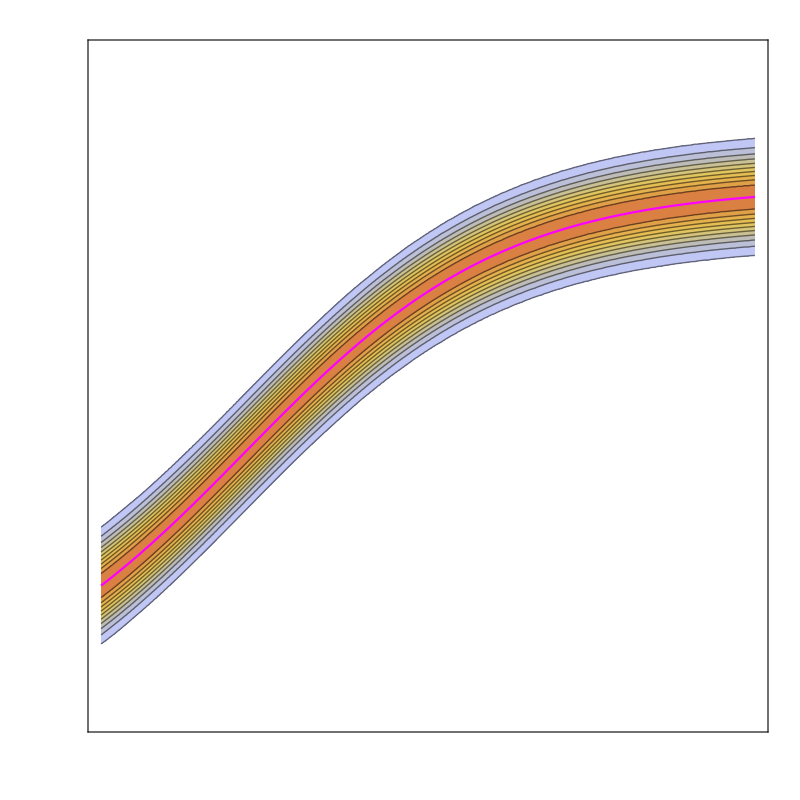

```mathematica
Show[ContourPlot[fPDF[y,x,0.5,0.05,5,fSigma],{x,0,10},{y,0,25},PlotPoints->50,PlotRange->Full,ColorFunction->(ColorData[{"BeachColors","Reverse"}][#]&),Contours->10,Axes->None,FrameLabel->None,ImageSize->800,FrameTicks->None,FrameStyle->Directive[Black,16,Thick],Frame->{True,True,False,False}],Plot[fMean[x,0.5,0.05,5],{x,0,10},PlotStyle->Magenta]]
```

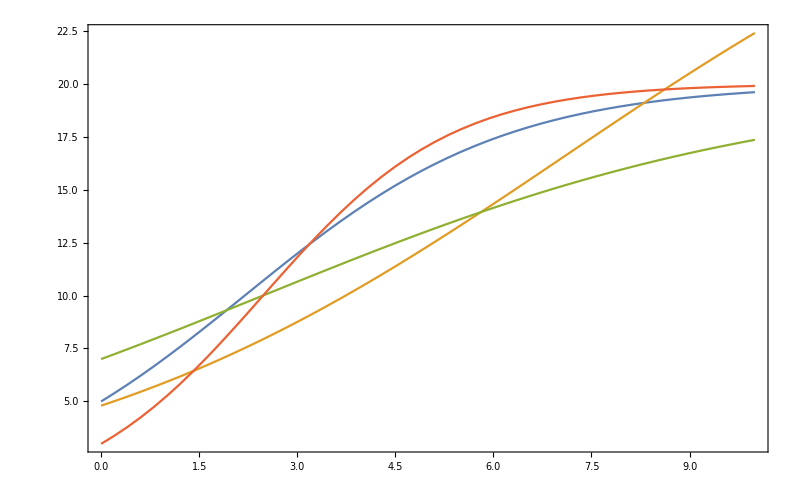

```mathematica
g1=Plot[{fMean[x,0.5,0.05,5],fMean[x,0.25,0.03,4.8],fMean[x,0.25,0.05,7],fMean[x,0.7,0.05,3]},{x,0,10},FrameLabel->None,ImageSize->800,FrameTicks->None,FrameStyle->Directive[Black,16,Thick],Frame->{True,True,False,False}]
```